```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,a,p,aa,bb]
```

```mathematica
(* F. M. Dekking, "Recurrent Sets" ,Advances in Mathematics,vol. 44, no.1,April 1982, page 85, section 4.15*)
```

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
(*Minimal Pisot Polynomial*)
```

```mathematica
m=Transpose[CompanionMatrix[-36 x^3+105 x^4-112 x^5+54 x^6-12 x^7+x^8,x]]
```

{{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1},{0,0,0,36,-105,112,-54,12}}

```mathematica
n0=8
```

8

```mathematica
(* substitution *)
```

```mathematica
Clear[s]
```

```mathematica
s[1]={1,6,3,1,0,0,0,0,0,0,0,0,0,0,0,0};
 s[2]={2,4,5,2,0,0,0,0,0,0,0,0,0,0,0,0}; 
s[3]={3,1,2,4,0,0,0,0,0,0,0,0,0,0,0,0}; 
s[4]={3,1,2,4,0,0,0,0,0,0,0,0,0,0,0,0};s[5]={5,2,7,5,0,0,0,0,0,0,0,0,0,0,0,0};s[6]={6,8,1,6,0,0,0,0,0,0,0,0,0,0,0,0};s[7]={7,5,6,8,0,0,0,0,0,0,0,0,0,0,0,0};s[8]={7,5,6,8,0,0,0,0,0,0,0,0,0,0,0,0}
```

{7,5,6,8,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* make matrix*)
```

```mathematica
M0=Table[Table[Count[s[j],i],{i,1,n0}],{j,1,n0}]
```

{{2,0,1,0,0,1,0,0},{0,2,0,1,1,0,0,0},{1,1,1,1,0,0,0,0},{1,1,1,1,0,0,0,0},{0,1,0,0,2,0,1,0},{1,0,0,0,0,2,0,1},{0,0,0,0,1,1,1,1},{0,0,0,0,1,1,1,1}}

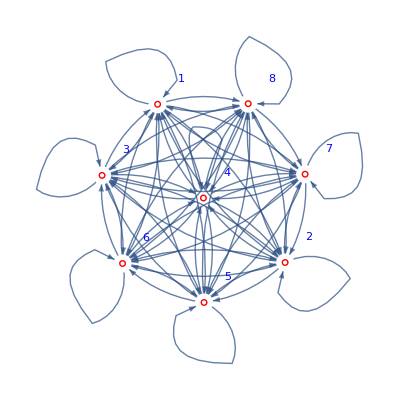

```mathematica
g=WeightedAdjacencyGraph[M0,VertexLabels->"Name",VertexSize->0.2,VertexShape->-Graphics-,VertexStyle->Blue]
```

```mathematica
{VertexList[g],EdgeList[g]}
```

{{1,2,3,4,5,6,7,8},{1->1,1->2,1->3,1->4,1->5,1->6,1->7,1->8,2->1,2->2,2->3,2->4,2->5,2->6,2->7,2->8,3->1,3->2,3->3,3->4,3->5,3->6,3->7,3->8,4->1,4->2,4->3,4->4,4->5,4->6,4->7,4->8,5->1,5->2,5->3,5->4,5->5,5->6,5->7,5->8,6->1,6->2,6->3,6->4,6->5,6->6,6->7,6->8,7->1,7->2,7->3,7->4,7->5,7->6,7->7,7->8,8->1,8->2,8->3,8->4,8->5,8->6,8->7,8->8}}

```mathematica
p[x_]=CharacteristicPolynomial[M0,x]
```

-36 x^3+105 x^4-112 x^5+54 x^6-12 x^7+x^8

```mathematica
(* make polynomial*)
```

```mathematica
Factor[Det[M0-x*IdentityMatrix[n0]]]
```

(-4+x) (-3+x)^2 (-1+x)^2 x^3

```mathematica
NSolve[p[x]==0,x]
```

{{x→0.},{x→0.},{x→0.},{x→1.},{x→1.},{x→3.},{x→3.},{x→4.}}

```mathematica
(*Substitution*)
```

```mathematica
(* 8 symbol *)
```

```mathematica
Clear[s]
s[1]={1,6,3,1};
 s[2]={2,4,5,2}; 
s[3]={3,1,2,4};
s[4]={3,1,2,4};s[5]={5,2,7,5};s[6]={6,8,1,6};s[7]={7,5,6,8};s[8]={7,5,6,8};
```

```mathematica
(*Reverse start vector*)
```

```mathematica
w=Reverse[Flatten[Table[s[i],{i,8}]]]
```

{8,6,5,7,8,6,5,7,6,1,8,6,5,7,2,5,4,2,1,3,4,2,1,3,2,5,4,2,1,3,6,1}

```mathematica
t[a_] :=Flatten[s/@a];         
p[0]=w;p[1]=t[p[0]];
p[n_]:=t[p[n-1]]
aa=p[6];
```

```mathematica
Length[aa]
```

131072

```mathematica
pts=N[{{1,0,1/2},{-1/2,(√3)/2,1/2},{-1/2,-(√3)/2,1/2},{0,0,3/2},{1,0,-1/2},{-1/2,(√3)/2,-1/2},{-1/2,-(√3)/2,-1/2},{0,0,-3/2}}];
```

```mathematica
bb=aa/. 1->pts[[1]]/. 2->pts[[2]]/. 3->pts[[3]]/. 4->pts[[4]]/. 5->pts[[5]]/. 6->pts[[6]]/. 7->pts[[7]] /. 8->pts[[8]];
```

```mathematica
cc=FoldList[Plus,{0,0,0},bb];
```

```mathematica
dd=ParallelTable[Cross[cc[[i]],cc[[i+1]]],{i,Length[cc]-1}];
```

```mathematica
g0=ListPointPlot3D[{dd,cc},ColorFunction->"Rainbow",Axes->False,PlotStyle->PointSize[0.001],ImageSize->2000,PlotRange->All];
```

```mathematica
Export["8symbol_Cross_vonKoch_substitution_Level6_start_vector3d_g0_3rd.jpg",g0]
```

8symbol_Cross_vonKoch_substitution_Level6_start_vector3d_g0_3rd.jpg

```mathematica
(* color seperation*)
```

```mathematica
allColors=ColorData["Legacy"][[3,1]];
firstCols={"Red","ManganeseBlue","Blue","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
(*cc=FoldList[Plus,{0,0},bb];*)
ee=Join[Flatten[ParallelTable[{cols[[aa[[n]]]],PointSize[0.001],Point[cc[[n]]]},{n,Min[Length[cc],Length[aa]]}]],Flatten[ParallelTable[{cols[[aa[[n]]]],PointSize[0.001],Point[dd[[n]]]},{n,Min[Length[dd],Length[aa]]}]]];
```

```mathematica
g2=Show[Graphics3D[ee],ImageSize->2000,Background->Black];
```

```mathematica
Export["8symbol_Cross_vonKoch_substitution_Level6_start_vector3d_g2_3rd.jpg",g2]
```

8symbol_Cross_vonKoch_substitution_Level6_start_vector3d_g2_3rd.jpg

```mathematica
Export["8symbol_Cross_VonKoch_substitution_Level6_start_vector3d_grid_3rd.jpg",GraphicsGrid[{{g0},{g2}},ImageSize->{2000,4000}]]
```

8symbol_Cross_VonKoch_substitution_Level6_start_vector3d_grid_3rd.jpg

```mathematica
(*end*)
```